# Quantum Fourier Transform: Semiclassical Implementation

Referencespaclet:Q3/tutorial/QuantumFourierTransformSemiclassical#890220681 | Testspaclet:Q3/tutorial/QuantumFourierTransformSemiclassical#1221384869
Demonstrationpaclet:Q3/tutorial/QuantumFourierTransformSemiclassical#2119699967 |

It is widely believed that the quantum entanglement is essential for quantum speed-up of quantum computation [1] or the precision measurement beyond the quantum standard limit (also known as the Heisenberg limit) [2]. The semiclassical implementation, to be demonstrated below, of the quantum Fourier transform (QFT) suggests that it is not necessarily the case.  In the semiclassical scheme, the single-qubit measurements and subsequent single-qubit gates controlled by the measurement results (classical signals) are sufficient to perform the QFT efficiently.

## References

[1] Griffiths & Niu, Physical Review Letters 76, 3228 (1996).

[2] Higgins, et al., Nature 450, 393 (2007).

## Demonstration

First, load the package.

```mathematica
<<Q3`
```

Choose the symbol S to represent qubits.

```mathematica
Let[Qubit,S]
```

```mathematica
$N=5;
ss=S[Range[$N],None]
```

{S_1,S_2,S_3,S_4,S_5}

Here are some handy functions to be used in the circuit implementations.

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,k-j],S[k],"Label"->Subscript["S",j-k]]
]/;j>k
CP[j_,k_]:=ControlledU[S[j],
Phase[Pi Power[2,j-k],S[k],"Label"->Subscript["S",k-j]]
]/;j<k
SW[j_]:=SWAP[S[j],S[$N-j+1]]
```

This is the typical QFT circuit explained in most textbooks.

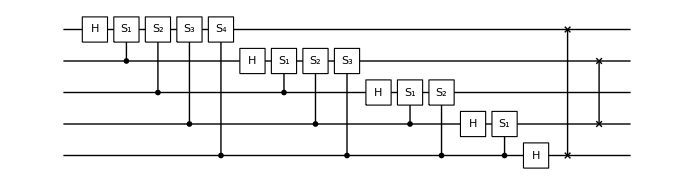

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$N},{j,k,$N}];
qft4a=Join[gates4a,swaps];
qc4a=QuantumCircuit[Sequence@@qft4a]
```

You can convince yourself that this circuit is equivalent to the above.

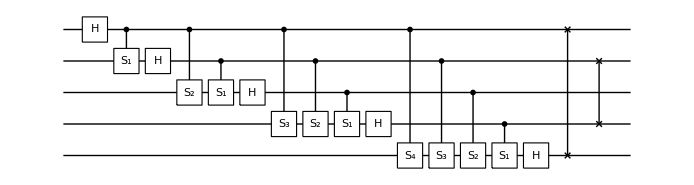

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$N},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuantumCircuit[Sequence@@qft4b]
```

Now consider measurements at the end of the calculation.

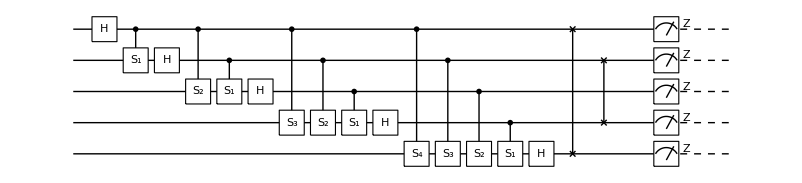

```mathematica
qft4c=Join[gates4b,swaps,{"Spacer",Measurement[Through[ss[3]]],"Spacer"}];
qc4c=QuantumCircuit[Sequence@@qft4c]
```

The measurements and SWAP gates can be exchanged. The resulting circuit is equivalent to the semiclassical implementation of the QFT as discussed in Ref. [1].

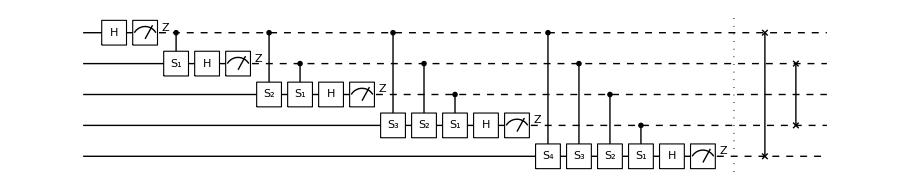

```mathematica
mm=Measurement/@Through[ss[3]];
mm=Transpose@{mm};
gates4d=Table[CP[j,k],{k,1,$N},{j,1,k}];
more=Catenate[Join@@@Thread[{gates4d,mm}]];
qft4d=Join[more,{"Separator"},swaps];
qc4d=QuantumCircuit[Sequence@@qft4d]
```

## Tests

```mathematica
mat4a=Matrix[qc4a];
mat4b=Matrix[qc4b];
mat4a-mat4b//N//Chop//Normal//Flatten
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

| Related Guides
▪Quisso Package Guide

| Related Tutorials
▪Quantum Computation and Quantum Information with Q3
▪QuantumCircuit Usage Examples
▪Quantum Fourier Transform
▪Quantum Teleportation

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/